# Problemi con potenziali centrali con Funzioni ipergemetriche

Problema 1) Andamento della soluzione Reale per una particella in caduta su di un centro, secondo il potenziale: U[r] = - β/r^2.


Problema 2) Se la funzione F[α, γ ; z] non ha i parametri in Z allora si hanno espressioni integrande come funzioni non modrome.
Esempio di parametri in Z:  dovrebbe uscire una funzione monodroma  (funzione che per ogni valore del dominio ammette un immagine)? 
Il dubbio e’ proprio sul senso della “trattazione” di Landau il quale dice che i valori in ogni punto sono supposti scelti con la condizione che l’ argomento della grandezza complessa elevato alla potenza sia minimo in modulo. Una possibile risposta sarebbe che: le funzioni polidrome non sono integrabili nel senso di Rienmann ed essendo curve γ[x(t),y(t)] nel piano (x,y) vedendo la (1) non si ha : lim(δ->0)S{f,P,t_i}=∫f[t]ⅆt.

Problema 3) Perche’ Mathematica non da espressioni analitiche per F[α,γ; z] con parametri non in Z, pero’ le plotta? Possibile siano numeriche? perche’ le espressioni integrande sono polinomi  a esponenti  parametrizzati (P[α,γ; z] )per esponenziali.

---------------------------------------------------------------------------------------------------------------------------------------------------------

Per la prima espressione ho studiato al variare dei parametri {a = r_0, γ = 2mβ/(ℏ)-l(l-1),c=1} (pongo la costante davanti all’ espressione =1 )la soluzione per una funzione d’ onda appartenente ad una particella in un moto di caduta su di un centro (si nota r_0 -> 0 gli zeri crescono e il comportamento per r - >∞ e quello di un oscillazione con λ per ogni cresta che cresce in (r))

```mathematica
Manipulate[Plot[{ 1/(r)^(1/2)*Cos[(γ-1/4)^(1/2) Log[r/a]+c],Log[r/a]},{r,-0.001,0.0001},
PlotRange->{-100,100}],{a,-1,10},{γ,1/4,10},{c,1}]
```

Scrivo ora la soluzione per la funzione d’ onda dell’ equazione di Schrödiger del problema potenziale coulombiano (U(r) = ±α/r).
In questo modo scrivendo in coordinate sferiche l’ equazione differenziale e risolvendo per la 

ψ[r,θ,ϕ] = R[r]Y[θ,ϕ] ;

e ponendo 

R[ρ]=ρ^l  Exp[-ρ/2]w[ρ] ;

ottengo la sottostante funzione ipergeometrica confluente:

F[α,γ; z] = -1/(2π i) (Γ[1-α]Γ[γ])/Γ[γ-α]∫_C Exp[t z](-t)^(α-1)  (1-t)^(γ-α-1)ⅆt ,

 F[α,γ; z] = Γ[γ]/(Γ[α]Γ[γ-α])∫_0^1 Exp[zt](t)^(α-1)  (1-t)^(γ-α-1)ⅆt .

```mathematica
Manipulate[Hypergeometric1F1[-n+l+1,2l+2,x],
{{n,-10,Dynamic@Panel[Row[{Style["n= ",Blue,14],Style[n,Blue,14]}],ImageSize->{80,40}]},
{0,1,2,3,4,10}},{l,0,10}]
```

Plot delle funzioni ipergeometriche del tipo soprastante. Si puo’ provare con valori per α e γ appartenenti a  qualunque campo.

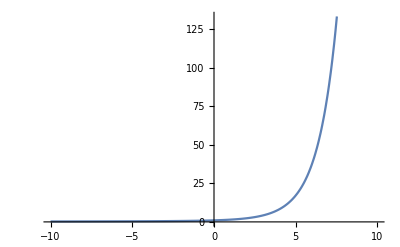

```mathematica
Plot[{Hypergeometric1F1[0.5,1.5,x]},
{x,-10,10},
PlotLegends->"Expressions"]
```

Esempio:
Considero una funzione polidroma integranda per una funzione ipergeometrica  F[α,γ; z] a coefficienti α =3/2 e γ =1/2.
In questo caso ottengo come risultato dell’ integrale una funzione proporzionale alla funzione di  Dawson.

(ⅇ^a DawsonF[√a])/(√a)

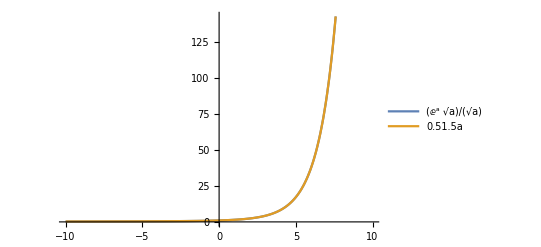

```mathematica
Gamma[3/2]/(Gamma[1/2]Gamma[3/2-1/2])∫_0^1 (Exp[a*t] (t)^(-1/2))ⅆt

Plot[{(ⅇ^a DawsonF[√a])/(√a),Hypergeometric1F1[0.5,1.5,a]},{a,-10,10},PlotLegends->"Expressions"]
```